```mathematica
M=5;
Subscript[ϕ, 1][x_]:=1;
Subscript[ϕ, 2][x_]:=√3 x;
Subscript[ϕ, 3][x_]:=(√5)/2(3 x^2-1)
Subscript[ϕ, 4][x_]:=(√7)/2( 5 x^3-3  x)
Subscript[ϕ, 5][x_]:=105/8 x^4-45/4 x^2+9/8
η[x_]:=(∑_(l=1)^M Subscript[Q, l]*Subscript[ϕ, l][x])^3
```

```mathematica
integral[k_,l_]:=∫_-1^1 η[x]*Subscript[ϕ, k][x]*ReplaceAll[D[Subscript[ϕ, l][x1],x1],x1->x]ⅆx
```

```mathematica
Table[integral[k,l],{k,1,M},{l,1,M}]//MatrixForm
```

```mathematica
Table[integral[k,1],{k,1,M}]//TableForm
```

0
0
0
0
0

```mathematica
Table[integral[k,2],{k,1,M}]//TableForm
```

√3 (2 Q_1^3+6 Q_1 (Q_2^2+Q_3^2+Q_4^2+Q_5^2)+(4 (3003 √5 Q_2^2 Q_3+715 √5 Q_3^3+6435 Q_3^2 Q_5+143 √21 Q_2 Q_4 (9 √5 Q_3+20 Q_5)+45 Q_5 (91 Q_4^2+27 Q_5^2)+26 √5 Q_3 (77 Q_4^2+75 Q_5^2)))/5005)
(2 (15015 √3 Q_1^2 Q_2+9009 √3 Q_2^3+7722 √7 Q_2^2 Q_4+6 √7 Q_4 (2145 Q_3^2+546 Q_4^2+1846 √5 Q_3 Q_5+1530 Q_5^2)+13 √3 Q_2 (1815 Q_3^2+1771 Q_4^2+792 √5 Q_3 Q_5+1755 Q_5^2)+858 Q_1 (14 √15 Q_2 Q_3+√7 Q_4 (9 √5 Q_3+20 Q_5))))/5005
(2 √(3/5) (3003 √5 Q_1^2 Q_3+2145 √5 Q_3^3+5551 √5 Q_3 Q_4^2+7020 Q_3^2 Q_5+10332 Q_4^2 Q_5+5367 √5 Q_3 Q_5^2+2700 Q_5^3+429 Q_2^2 (11 √5 Q_3+12 Q_5)+52 √21 Q_2 Q_4 (33 √5 Q_3+71 Q_5)+26 Q_1 (231 Q_2^2+165 Q_3^2+99 √21 Q_2 Q_4+154 Q_4^2+198 √5 Q_3 Q_5+150 Q_5^2)))/1001
1/715 ((5148 Q_2^3)/(√7)+6578 √3 Q_2^2 Q_4+(12 Q_2 (2145 Q_3^2+1638 Q_4^2+13 √5 Q_3 (99 Q_1+142 Q_5)+10 Q_5 (286 Q_1+153 Q_5)))/(√7)+2 √3 Q_4 (3965 Q_3^2+1687 Q_4^2+8 √5 Q_3 (143 Q_1+369 Q_5)+15 (143 Q_1^2+156 Q_1 Q_5+291 Q_5^2)))
(2 √3 (1989 Q_2^2 (44 √5 Q_3+195 Q_5)+68 √21 Q_2 Q_4 (1430 Q_1+923 √5 Q_3+1530 Q_5)+3 (13260 √5 Q_3^3+85085 Q_1^2 Q_5+152065 Q_3^2 Q_5+173145 Q_4^2 Q_5+71415 Q_5^3+204 √5 Q_3 (287 Q_4^2+225 Q_5^2)+170 Q_1 (429 Q_3^2+273 Q_4^2+260 √5 Q_3 Q_5+243 Q_5^2))))/85085

```mathematica
Table[integral[k,3],{k,1,M}]//TableForm
```

3 √5 (2 √3 Q_1^2 Q_2+4/35 Q_1 (14 √15 Q_2 Q_3+√7 Q_4 (9 √5 Q_3+20 Q_5))+(2 (9009 √3 Q_2^3+7722 √7 Q_2^2 Q_4+6 √7 Q_4 (2145 Q_3^2+546 Q_4^2+1846 √5 Q_3 Q_5+1530 Q_5^2)+13 √3 Q_2 (1815 Q_3^2+1771 Q_4^2+792 √5 Q_3 Q_5+1755 Q_5^2)))/15015)
(2 √(3/5) (5005 Q_1^3+6006 √5 Q_1^2 Q_3+13 Q_1 (2079 Q_2^2+1815 Q_3^2+396 √21 Q_2 Q_4+1771 Q_4^2+792 √5 Q_3 Q_5+1755 Q_5^2)+2 (2860 √5 Q_3^3+13455 Q_3^2 Q_5+2574 Q_2^2 (3 √5 Q_3+2 Q_5)+273 √21 Q_2 Q_4 (11 √5 Q_3+24 Q_5)+9 Q_5 (1603 Q_4^2+435 Q_5^2)+√5 Q_3 (7553 Q_4^2+7317 Q_5^2))))/1001
(10296 √3 Q_2^3+18018 √7 Q_2^2 Q_4+6 √7 Q_4 (1287 Q_1^2+52 Q_1 (33 √5 Q_3+71 Q_5)+7 (585 Q_3^2+207 Q_4^2+464 √5 Q_3 Q_5+549 Q_5^2))+4 √3 Q_2 (7553 Q_4^2+3 (1001 Q_1^2+2860 Q_3^2+1716 Q_1 Q_5+2439 Q_5^2+13 √5 Q_3 (121 Q_1+138 Q_5))))/1001
(3978 Q_2^2 (66 Q_1+77 √5 Q_3+168 Q_5)+68 √21 Q_2 Q_4 (3289 Q_1+2158 √5 Q_3+4122 Q_5)+6 (2431 Q_1^2 (9 √5 Q_3+20 Q_5)+7 (3315 √5 Q_3^3+19720 Q_3^2 Q_5+24888 Q_4^2 Q_5+8640 Q_5^3+153 √5 Q_3 (69 Q_4^2+61 Q_5^2))+34 Q_1 (2145 Q_3^2+1846 √5 Q_3 Q_5+18 (91 Q_4^2+85 Q_5^2))))/(2431 √35)
(12 (9724 √3 Q_2^3+55692 √7 Q_2^2 Q_4+51 √3 Q_2 (1495 Q_3^2+1603 Q_4^2+15 Q_5 (169 Q_1+87 Q_5)+2 √5 Q_3 (286 Q_1+813 Q_5))+√7 Q_4 (24310 Q_1^2+34 Q_1 (923 √5 Q_3+1530 Q_5)+7 (9860 Q_3^2+4148 Q_4^2+9333 √5 Q_3 Q_5+12960 Q_5^2))))/(17017 √5)

```mathematica
%//MatrixForm//FullSimplify
```

(0 | √3 (2 Q_1^3+6 Q_1 (Q_2^2+Q_3^2)+(4 Q_3 (21 Q_2^2+5 Q_3^2))/(7 √5)) | 6/7 √(3/5) Q_2 (35 Q_1^2+21 Q_2^2+28 √5 Q_1 Q_3+55 Q_3^2)
0 | 6/35 √3 Q_2 (35 Q_1^2+21 Q_2^2+28 √5 Q_1 Q_3+55 Q_3^2) | 2/35 √3 (35 √5 Q_1^3+210 Q_1^2 Q_3+540 Q_2^2 Q_3+200 Q_3^3+3 √5 Q_1 (63 Q_2^2+55 Q_3^2))
0 | 6/35 √3 (35 Q_1^2 Q_3+55 Q_2^2 Q_3+25 Q_3^3+2 √5 Q_1 (7 Q_2^2+5 Q_3^2)) | 12/7 √3 Q_2 (7 Q_1^2+6 Q_2^2+11 √5 Q_1 Q_3+20 Q_3^2))

```mathematica
∫_-1^1 ReplaceAll[D[Subscript[ϕ, 3][x1],x1],x1->x]*Subscript[ϕ, 3][x]ⅆx
```

0

```mathematica
∫_-1^1 Subscript[ϕ, 5][x]ⅆx
```

(2 a)/5+(2 b)/3+2 c

```mathematica
∫_-1^1 Subscript[ϕ, 5][x]*Subscript[ϕ, 3][x]ⅆx
```

(8 a)/(7 √5)+(4 b)/(3 √5)

```mathematica
∫_-1^1 Subscript[ϕ, 5][x]*Subscript[ϕ, 5][x]ⅆx
```

(2 a^2)/9+(4 a b)/7+(2 b^2)/5+(4 a c)/5+(4 b c)/3+2 c^2

```mathematica
Solve[{(2 a)/5+(2 b)/3+2 c==0,(8 a)/(7 √5)+(4 b)/(3 √5)==0,(2 a^2)/9+(4 a b)/7+(2 b^2)/5+(4 a c)/5+(4 b c)/3+2 c^2==2},{a,b,c}]
```

{{a→-105/8,b→45/4,c→-9/8},{a→105/8,b→-45/4,c→9/8}}

```mathematica
Table[∫_-1^1 Subscript[ϕ, k][x]Subscript[ϕ, l][x]ⅆx,{k,1,M},{l,1,M}]//MatrixForm
```

(2 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 2)

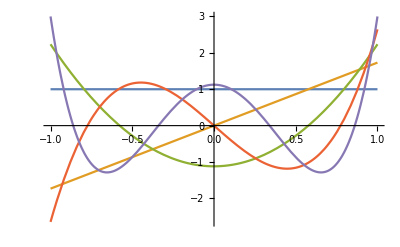

```mathematica
Plot[{Subscript[ϕ, 1][x],Subscript[ϕ, 2][x],Subscript[ϕ, 3][x],Subscript[ϕ, 4][x],Subscript[ϕ, 5][x]},{x,-1,1}]
```